Carbapenem Resistance Model:

Objective: Whereas a clear correlation exists between consumption of antibiotics and the evolution of resistance in microbial communities, the effect of reduction of usage is less clear. To project the future frequency of carbapenem resistance, based on yearly surveillance data and consumption data. A population genetic model was adapted to retrospectively estimate the relationship between evolutionary fitness of carbapenem resistance and carbapenem consumption.

Derivation: We fit the historical selection to consumption via a deterministic, continuous-time haploid model of the frequency of resistance. See, for reference: 1) Hartl, Daniel L., Andrew G. Clark, and Andrew G. Clark. Principles of population genetics. Vol. 116. Sunderland: Sinauer associates, 1997—base population genetic model; 2) Nielsen, K. M., & Townsend, J. P. (2004). Monitoring and modeling horizontal gene transfer. Nature biotechnology, 22(9), 1110-1114—relation of base model to novel DNA such as antimicrobial resistance elements; and 3) Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610 —application of base model to project future vancomycin resistance after ban of use.

```mathematica
Note that the likelihood function used here will additionally be improved from that used in the preliminary model above. Because surveillance is conducted by sampling and testing for resistance, likelihood can be quantified under better distributional assumptions, with greater accuracy and precision. Instead of the observed frequencies of resistance (which are not certain), likelihood can be calculated based on the observed cases of resistant (UKResistance, above) vs. non-resistant (UKIsolates – UKResistance, above) measured by surveillance—see for instance, Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610.
```

First, we test the simple model with two selection coefficients:

(1) a = the growth rate of resistant Klebsiella that are exposed to carbapenems--i.e. under positive selection conditions,

(2) d = the growth rate of nonresistant Klebsiella that are not exposed to carbapenems--i.e. natural growth rate with no selection.

We make the following assumptions:

(1) All nonresistant Klebsiella that are exposed to carbapenems will die (growth rate=0)

(2) Resistant Klebsiella that are not exposed to carbapenems will also have a growth rate of 0

(3) Alternative treatments are not effective

(4) All consumption data is for the community sector only

(5) No co-selection of resistance

```mathematica
ClearAll["Global`*"]
```

```mathematica
Load Data
```

Number of resistant isolates recovered, each year 2005–2014; Number of isolates tested, each year 2005–2014, estimated frequencies of resistance, 2005–2014.

```mathematica
Where c = country-wide consumption of carbapenems (DDD/1000 patient-days); TotalAb = country-wide total antibiotic consumption (DDD/1000 patient-days); Isolates = number of K. pneumoniae isolates tested for resistance; Resistance = number of isolates resistant; p = prescription guideline for carbapenems = [c(t) * of carbapenems used how many are prescribed to Klebsiella] / [total antibiotic use * of antibiotics used how many are prescribed to Klebsiella] = (c * fc) / (TotalAb * fa); note that fc and fa will be informed by data, but for now we're just assuming values
```

```mathematica
SetDirectory[NotebookDirectory[]];
CountryName="France";
Data=Import["DataSheet.xlsx",{"Data",CountryName}];
c=Drop[Data[[2]],1];
TotalAb=Drop[Data[[5]],1];
Isolates=Drop[Data[[3]],1];
Resistance=Drop[Data[[4]],1];
RData=Resistance/Isolates;

fc=0.001;
fa=0.001;
p= (c*fc)/(TotalAb*fa)
```

{0.,0.0000179211,0.0000594406,0.0000640569,0.0000608108,0.000070922,0.000108014,0.00013468,0.000146179,0.000155172}

```mathematica
Model Definitions: r is the frequency of resistance at time t, r0 is the initial frequency of resistance, p is the proportion of carbapenems prescribed, and m is the continuous time Malthusian selection coefficients for resistant K. pneumoniae relative to non-resistant.  [Make them work]
```

```mathematica
r[t_,a_,d_,r0_]:= If[t==1,r0,RecurrenceTable[{md[n+1] ==ⅇ^((p[[t]]*md[n]*a)/((1-p[[t]])*(1 - md[n]*d)*(n+1)))/((1/r0)-1+ⅇ^((p[[t]]*md[n]*a)/((1 - p[[t]])*(1 - md[n])*d)*(n+1))),md[1]==r0},md,{n,1,t}][[-1]]]
r[10,0.900494,1,0.9]
```

0.890826

```mathematica
Maximum Likelihood Function
```

```mathematica
Lik[a_,d_,r0_]:= Total[Table[Log[Binomial[Isolates[[j]],Resistance[[j]]]]+Resistance[[j]]*Log[r[j-1,a,d,r0]]+(Isolates[[j]]-Resistance[[j]])*Log[1-r[j-1,a,d,r0]],{j,2,10}]]
Lik[0.900494,1.,0.9]
```

-28518.9

```mathematica
{max,{fitr0,fita,fitd}}=FindMaximum[{Lik[a,d,r0],a≥ 0,1≥ d≥ 0,0.005≤ r0≤1},{a,d,r0}]
```

Plot over time

```mathematica
Years=Range[2005,2014];
Res=Transpose@{Years,RData};
t=Range[1,10];
ModelFit=Transpose@{Years,r[t,fitr0[[2]],fita[[2]],fitd[[2]]]};
```

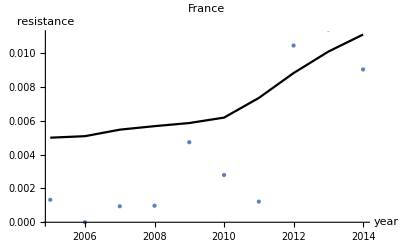

```mathematica
plot1=ListLinePlot[ModelFit, PlotStyle-> {Black},AxesLabel->{year,resistance},PlotLabel-> France, PlotRange-> All];
plot2=ListPlot[{Res}, PlotStyle-> PointSize[Large],PlotRange-> All];
Show[plot1,plot2]
```